Integrate[w*E^(I*w*(t )), w]

WolframAlphaQueryResults

```mathematica
Simplify[ⅇ^(ⅈ (t-t2) w) (1/(t-t2)^2-(ⅈ w)/(t-t2))]
```

(ⅇ^(ⅈ (t-t2) w) (1-ⅈ t w+ⅈ t2 w))/(t-t2)^2

```mathematica
Simplify[ⅇ^(ⅈ t w) (1/t^2-(ⅈ w)/t)]
```

(ⅇ^(ⅈ t w) (1-ⅈ t w))/t^2

```mathematica
Integrate[A*E^-(A*I*x)-B*E^-(A*I*x),{x,-Infinity,0}]
```

ConditionalExpression[(ⅈ (A-B))/A, Im[A]>0]

```mathematica
Integrate[A ⅇ^(A ⅈ x)-B ⅇ^(A ⅈ x),{x,-∞,∞},PrincipalValue->True]
```

0

```mathematica
Integrate[E^(I*x*t),t]
```

-(ⅈ ⅇ^(ⅈ t x))/x

```mathematica
Limit[-(ⅈ (A-B) ⅇ^(-ⅈ *A *x))/A,x ->Infinity]
```

lim_(x→∞) -(ⅈ (A-B) ⅇ^(-ⅈ A x))/A

```mathematica
lim_(x->∞) -(ⅈ (A-B) ⅇ^(ⅈ A x))/A
```

lim_(x→∞) -(ⅈ (A-B) ⅇ^(ⅈ A x))/A

```mathematica
Simplify[lim_(x->∞) -(ⅈ (A-B) ⅇ^(ⅈ A x))/A]
```

lim_(x→∞) -(ⅈ (A-B) ⅇ^(ⅈ A x))/A

```mathematica
Integrate[E^(I*w*(t-t2)),{t2,0,t}]
```

-(ⅈ (-1+ⅇ^(ⅈ t w)))/w

```mathematica
Integrate[E^(I*w*(t-t2))-E^(g^2*(t-t2)),{t2,0,t}]
```

(1-ⅇ^(g^2 t))/g^2-(ⅈ (-1+ⅇ^(ⅈ t w)))/w

```mathematica
ContourPlot3D[Evaluate[ReIm[(1 - E^(g^2*t))/g^2 - (I*(-1 + E^(I*t*w)))/w]], {g, 1., 6.}, {t, -6., 6.}, {w,0,2}]
```

-Graphics3D-

```mathematica
Integrate[g/(w-w2)*E^(I*w*(t-t2)),{w,-Infinity,Infinity}]
```

ConditionalExpression[g (Cos[((t-t2) w2)/Sign[t-t2]] (-Log[-w2]+Log[w2]+ⅈ π Sign[t-t2])-(π+ⅈ (Log[-w2]-Log[w2]) Sign[t-t2]) Sin[((t-t2) w2)/Sign[t-t2]]), Im[t]==Im[t2]&&w2≠Re[w2]]

```mathematica
g1=((n+1)*E^(-I*w*(t1-t2))/I)
g2=((n)*E^(-I*w*(t1-t2))/I)
```

-ⅈ ⅇ^(-ⅈ (t1-t2) w) (1+n)

-ⅈ ⅇ^(-ⅈ (t1-t2) w) n

```mathematica
g2+g1
```

-ⅈ ⅇ^(-ⅈ (t1-t2) w) n-ⅈ ⅇ^(-ⅈ (t1-t2) w) (1+n)

```mathematica
Simplify[-ⅈ ⅇ^(-ⅈ (t1-t2) w) n-ⅈ ⅇ^(-ⅈ (t1-t2) w) (1+n)]
```

-ⅈ ⅇ^(-ⅈ (t1-t2) w) (1+2 n)

```mathematica
(1/(e^x-1))^(-1)
```

-1+e^x

```mathematica
Integrate[(I*2*g )/((w-wo)^2+g^2)E^(I*w*(t-t2)),{w,0,+Infinity}]
```

ConditionalExpression[ⅇ^(-((t-t2) (g-ⅈ wo))) (Gamma[0,-((t-t2) (g-ⅈ wo))]-Log[-ⅈ (t-t2)]+Log[-((t-t2) (g-ⅈ wo))]+Log[-1/(ⅈ g+wo)]+ⅇ^(2 g (t-t2)) (CoshIntegral[(t-t2) (g+ⅈ wo)]+Log[-ⅈ (t-t2)]-Log[(t-t2) (g+ⅈ wo)]-Log[-1/(-ⅈ g+wo)]-SinhIntegral[(t-t2) (g+ⅈ wo)])), ]

```mathematica
FourierTransform[(1)/((w-wo)+I*g),w,(t-t2),Assumptions->{Element[{t,t2,w,wo,g},PositiveReals]}]
```

-ⅈ ⅇ^((t-t2) (g+ⅈ wo)) √(2 π) HeavisideTheta[-t+t2]

```mathematica
Simplify[-ⅈ ⅇ^((t-t2) (g+ⅈ wo)) √(π/2) (2 HeavisideTheta[(-t+t2) Sign[g]] Sign[g]+Sign[t-t2] (-1+Sign[Abs[g]]))]
```

```mathematica
FourierTransform[(2*I*g(nb+1))/((w-wo)^2+g^2),w,(t-t2),Assumptions->{Element[{t,t2,w,wo,g,nb},PositiveReals]}]
```

ⅈ ⅇ^(-((t-t2) (g-ⅈ wo))) (1+nb) √(2 π) (HeavisideTheta[t-t2]+ⅇ^(2 g (t-t2)) HeavisideTheta[-t+t2])

```mathematica
Integrate[ⅈ ⅇ^(-((t-t2) (g-ⅈ wo))) (1+nb) √(2 π) (HeavisideTheta[t-t2]+ⅇ^(2 g (t-t2)) HeavisideTheta[-t+t2]),{t,0,t2}]
```

(ⅈ (1-ⅇ^(-t2 (g+ⅈ wo))) (1+nb) √(2 π))/(g+ⅈ wo)

```mathematica
1/(w1-w2-I*g)-1/(w1-w2+I*g)
```

1/(-ⅈ g+w1-w2)-1/(ⅈ g+w1-w2)

```mathematica
Simplify[1/(-ⅈ g^2+w1-w2)-1/(ⅈ g^2+w1-w2)]
```

(2 ⅈ g^2)/(g^4+(w1-w2)^2)

```mathematica
FourierTransform[(2 ⅈ g^2)/(g^4+(w1-w2)^2),w1,t]
```

ⅈ ⅇ^(-t (g^2-ⅈ w2)) √(π/2) (Sign[t] (1-ⅇ^(2 g^2 t)+ⅇ^(2 g^2 t) Sign[Abs[Im[w2]-Re[g^2]]]-Sign[Abs[Im[w2]+Re[g^2]]])+2 (ⅇ^(2 g^2 t) HeavisideTheta[t Sign[Im[w2]-Re[g^2]]] Sign[-Im[w2]+Re[g^2]]+HeavisideTheta[t Sign[Im[w2]+Re[g^2]]] Sign[Im[w2]+Re[g^2]]))

```mathematica
FourierTransform[(2 (w1-w2))/(g^4+(w1-w2)^2),w1,t,Assumptions->g>0]
```

-ⅈ ⅇ^(-t (g^2-ⅈ w2)) √(π/2) (Sign[t] (-1-ⅇ^(2 g^2 t)+ⅇ^(2 g^2 t) Sign[Abs[g^2-Im[w2]]]+Sign[Abs[g^2+Im[w2]]])+2 ⅇ^(2 g^2 t) HeavisideTheta[-t Sign[g^2-Im[w2]]] Sign[g^2-Im[w2]]-2 HeavisideTheta[t Sign[g^2+Im[w2]]] Sign[g^2+Im[w2]])

```mathematica
FourierTransform[(2 ⅈ g)/(g^2+(w1-w2)^2),w1,t,Assumptions->g>0,0]
```

```mathematica
FourierTransform[(2 ⅈ g)/(g^2+(w1-w2)^2),w1,t]
```

ⅈ ⅇ^(-t (g-ⅈ w2)) √(π/2) (Sign[t] (1-ⅇ^(2 g t)+ⅇ^(2 g t) Sign[Abs[Im[w2]-Re[g]]]-Sign[Abs[Im[w2]+Re[g]]])+2 (ⅇ^(2 g t) HeavisideTheta[t Sign[Im[w2]-Re[g]]] Sign[-Im[w2]+Re[g]]+HeavisideTheta[t Sign[Im[w2]+Re[g]]] Sign[Im[w2]+Re[g]]))

```mathematica
FourierTransform[(2 ⅈ g)/(g^2+(w1-w2)^2),w1,t]
```

ⅈ ⅇ^(-t (g-ⅈ w2)) √(π/2) (Sign[t] (1-ⅇ^(2 g t)+ⅇ^(2 g t) Sign[Abs[Im[w2]-Re[g]]]-Sign[Abs[Im[w2]+Re[g]]])+2 (ⅇ^(2 g t) HeavisideTheta[t Sign[Im[w2]-Re[g]]] Sign[-Im[w2]+Re[g]]+HeavisideTheta[t Sign[Im[w2]+Re[g]]] Sign[Im[w2]+Re[g]]))

```mathematica
FullSimplify[%2]
```

ⅈ ⅇ^(-t (g-ⅈ w2)) √(2 π) (ⅇ^(2 g t) HeavisideTheta[t Sign[Im[w2]-Re[g]]] Sign[-Im[w2]+Re[g]]+HeavisideTheta[t Sign[Im[w2]+Re[g]]] Sign[Im[w2]+Re[g]])

```mathematica
FourierTransform[g^2*E^(I*w*t),w,t]
```

FourierTransform[ⅇ^(ⅈ t w) g^2,w,t]

```mathematica
FourierTransform[g.b2 DiracDelta[w-w1],t,w]{g.b2,w,w1}
```

{FourierTransform[DiracDelta[w-w1],t,w],FourierTransform[ⅈ g.b2 t DiracDelta[w-w1],t,w],FourierTransform[-g.b2 DiracDelta'[w-w1],t,w]}

```mathematica
g*a+b
Clear[G]
```

(0.5+0.5 ⅈ)+b

```mathematica
G[t_,t1_]:=ⅇ^(-(g^2-ⅈ w)(t-t1))
```

```mathematica
w=1
g=0.5
```

1

0.5

```mathematica
0.5
a=-(1+I*1)
b[t_]:=Exp[-t*w]
```

0.5

-1-ⅈ

1

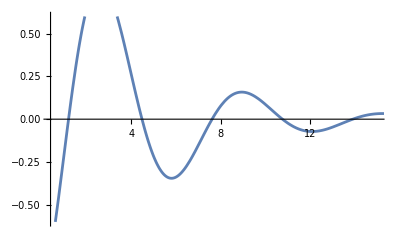

```mathematica
Plot[Re[a*G[t,0]-Integrate[G[t,t1]*b[t1],{t1,0,t}]],{t,0,25},PlotRange->{{0.4,15},{-0.6,0.6}}]
```

```mathematica
Int[G[t,t1]*b[t1],{t1,0,t}]
```

Int[ⅇ^((0.25-0.5 ⅈ) (t-t1)+0.5 t1),{t1,0,t}]

```mathematica
Simplify[Int[ⅇ^((0.25-0.5 ⅈ) (t-t1)+0.5 t1),{t1,0,t}]]
```

Int[ⅇ^((0.25-0.5 ⅈ) t+(0.25+0.5 ⅈ) t1),{t1,0,t}]

```mathematica
∫Int[ⅇ^((0.25-0.5 ⅈ) t+(0.25+0.5 ⅈ) t1),{t1,0,t}]ⅆt
```

∫Int[ⅇ^((0.25-0.5 ⅈ) t+(0.25+0.5 ⅈ) t1),{t1,0,t}]ⅆt

```mathematica
G[1,0]
```

1.12684-0.615595 ⅈ

```mathematica
a*G[t,0]*Integrate[G[t,t1]*b[t1],{t1,0,t}]
```

```mathematica
(1+ⅈ) ⅇ^((0.25-0.5 ⅈ) t) ((-0.8+1.6 ⅈ) ⅇ^((0.25-0.5 ⅈ) t)+(0.8-1.6 ⅈ) ⅇ^(0.5 t))
```